{1,2,3,4}

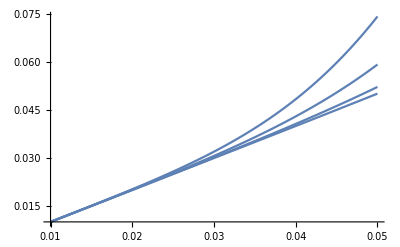

```mathematica
Λ := Subscript[λ, R]+(5 L (1+L))/(2 (-Subscript[ω, R]^2/(12 Subscript[λ, R])+(1/2 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))-√(Subscript[ω, R]^12/(4096 Subscript[λ, R]^6)+1/4 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))^2))^(1/3)+(1/2 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))+√(Subscript[ω, R]^12/(4096 Subscript[λ, R]^6)+1/4 ((L (1+L))/(4 Subscript[λ, R])+Subscript[ω, R]^6/(64 Subscript[λ, R]^3))^2))^(1/3))^3)
Subscript[ω, R]= 1.0;
L = {1,2,3,4}
Plot[Re[Λ],{Subscript[λ, R], 0.01, 0.05}]
```

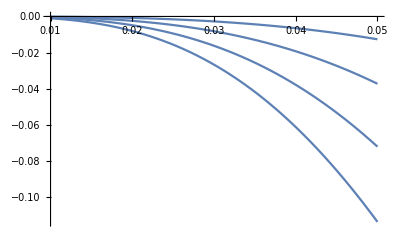

```mathematica
Plot[Im[Λ],{Subscript[λ, R], 0.01, 0.05}, PlotLegends->Automatic]
```